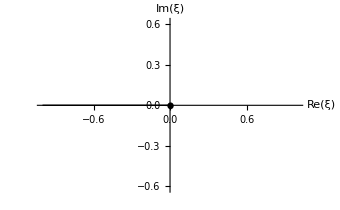

```mathematica
p1=Plot[ⅈ,{x,-1,1},AxesStyle->Dashed,Ticks->False,PlotStyle->{Black,Thick},AxesLabel->{Re[ξ],Im[ξ]},Epilog->{{Thick,Line[{{-1,0},{0,0}}]},Disk[{0,0},0.025]},AspectRatio->1/GoldenRatio,PlotRange->{{-1,1},{-1,1}/GoldenRatio},LabelStyle->{FontFamily->"Times",FontSize->12,Black},ImageSize->340]
```

```mathematica
Export["~/doc/research/first_order_singularities/paper/figs/F_lower_singularities.pdf",p1];
```

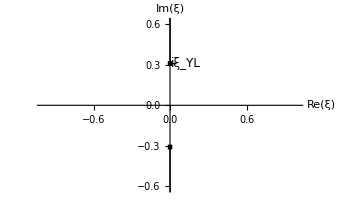

```mathematica
p2=Plot[ⅈ,{x,-1,1},AxesStyle->Dashed,Ticks->False,PlotStyle->{Black,Thick},AxesLabel->{Re[ξ],Im[ξ]},Epilog->{{Thick,Line[{{0,1/GoldenRatio/2},{0,1}}],Line[{{0,-1/GoldenRatio/2},{0,-1}}]},RegularPolygon[{0,1/GoldenRatio/2},0.025,4],RegularPolygon[{0,-1/GoldenRatio/2},0.025,4],
Line[{{0,1/GoldenRatio/2},{0.05,1/GoldenRatio/2}}],
{Black,Text[Style["iξ_YL",FontSize->12,Black,FontFamily->"Times"], {0.125,1/GoldenRatio/2}]}
},AspectRatio->1/GoldenRatio,PlotRange->{{-1,1},{-1,1}/GoldenRatio},LabelStyle->{FontFamily->"Times",FontSize->12,Black},ImageSize->340]
```

```mathematica
Export["~/doc/research/first_order_singularities/paper/figs/F_higher_singularities.pdf",p2];
```

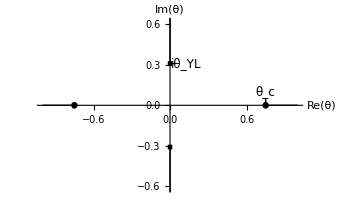

```mathematica
p3=Plot[ⅈ,{x,-1,1},AxesStyle->Dashed,Ticks->False,PlotStyle->{Black,Thick},AxesLabel->{Re[θ],Im[θ]},Epilog->{{Thick,Line[{{0,1/GoldenRatio/2},{0,1}}],Line[{{0,-1/GoldenRatio/2},{0,-1}}]},RegularPolygon[{0,1/GoldenRatio/2},0.025,4],RegularPolygon[{0,-1/GoldenRatio/2},0.025,4],{Thick,Line[{{-1,0},{-0.75,0}}]},Disk[{-0.75,0},0.025],{Thick,Line[{{1,0},{0.75,0}}]},Disk[{0.75,0},0.025],
Line[{{0.75,0},{0.75,0.05}}],
Line[{{0,1/GoldenRatio/2},{0.05,1/GoldenRatio/2}}],
{Black,Text[Style["iθ_YL",FontSize->12,Black,FontFamily->"Times"], {0.125,1/GoldenRatio/2}]},
{Black,Text[Style["θ_c",FontSize->12,Black,FontFamily->"Times"], {0.75,0.1}]}
},AspectRatio->1/GoldenRatio,PlotRange->{{-1,1},{-1,1}/GoldenRatio},LabelStyle->{FontFamily->"Times",FontSize->12,Black},ImageSize->340]
```

```mathematica
Export["~/doc/research/first_order_singularities/paper/figs/F_theta_singularities.pdf",p3];
```

```mathematica
p4=Plot[√(0.95^2-x^2)/GoldenRatio,{x,-1,1},AxesStyle->Dashed,Ticks->False,PlotStyle->{Red},AxesLabel->{Re[θ'],Im[θ']},Prolog->{
{Thickness[0.005],Red,Line[{{-0.95,0.0115},{-0.8,0.0115}}]},
{Thickness[0.005],Red,Circle[{-0.75,0},0.05,{0,π}]},
{Thickness[0.005],Red,Line[{{0.8,0.0115},{0.95,0.0115}}]},
{Thickness[0.005],Red,Circle[{0.75,0},0.05,{0,π}]},
{Thickness[0.005],Red,Line[{{-0.7,0},{0.-0.05,0}}]},
{Thickness[0.005],Red,Circle[{0,0},0.05,{0,π}]},
{Thickness[0.005],Red,Line[{{0.05,0},{0.25,0}}]},
{Thickness[0.005],Red,Circle[{0.3,0},0.05,{0,π}]},
{Thickness[0.005],Red,Line[{{0.35,0},{0.7,0}}]},
{Thickness[0.005],Red,Line[{{0.0115,1/GoldenRatio 0.95},{0.0115,1/GoldenRatio/2+0.05}}]},
{Thickness[0.005],Red,Line[{{-0.0115,1/GoldenRatio 0.95},{-0.0115,1/GoldenRatio/2+0.05}}]},
{Thickness[0.005],Red,Circle[{0,1/GoldenRatio/2},0.05]},
Line[{{0.3,0},{0.3,-0.05}}],
{Black,Text[Style["θ",FontSize->12,Black,FontFamily->"Times"], {0.3,-0.1}]}},
Epilog->{
{Thick,Line[{{0,1/GoldenRatio/2},{0,1}}],Line[{{0,-1/GoldenRatio/2},{0,-1}}]},RegularPolygon[{0,1/GoldenRatio/2},0.025,4],
Rotate[RegularPolygon[{0,0},0.025,4],π/4],RegularPolygon[{0,-1/GoldenRatio/2},0.025,4],{Thick,Line[{{-1,0},{-0.75,0}}]},Disk[{-0.75,0},0.025],{Thick,Line[{{1,0},{0.75,0}}]},Disk[{0.75,0},0.025],
Polygon[{0.3,0}+#&/@SortBy[0.025/1.5Join[CirclePoints[5],-CirclePoints[5]/2],ArcTan@@#&]]
},AspectRatio->1/GoldenRatio,PlotRange->{{-1,1},{-1,1}/GoldenRatio},LabelStyle->{FontFamily->"Times",FontSize->12,Black},ImageSize->340]
```

-Graphics-

```mathematica
Export["~/doc/research/first_order_singularities/paper/figs/contour_path.pdf",p4];
```

```mathematica
ComplexExpand[Re[1/((t-ξ)ⅈ t)],{t}]/.Im[t]->0
```

0

```mathematica
ComplexExpand[Re[ⅈ/((ⅈ t-ξ)(ⅈ t)^2)]]
```

-1/(t (t^2+ξ^2))

```mathematica
iF1[θc_,B_][x_]:=(x-θc) Exp[-1/(B(x-θc))]
```

```mathematica
iii2=θ^2/π Integrate[((x^2+θ0^2)^(5/6))/x^2(1/(x-θ)+1/(x+θ)),{x,θc,∞},Assumptions->{θ<θc,θ>0,θc>0,B>0,θ0>0,θ0<θc}]
```

$Aborted

```mathematica
Series[iF1[θc,B][x],{θ,θc,1}]
```

ⅇ^(-1/(B (x-θc))) (x-θc)

```mathematica
Series[t[θ]^2 ξ Exp[-1/(b ξ)]/.ξ->(θ h'[θ])/t[θ]^(15/8),{θ,0,1}]
```

ⅇ^(-t[0]^(15/8)/(b h'[0] θ)+(-(15 t[0]^(7/8) t'[0])/(8 h'[0])+(t[0]^(15/8) h''[0])/h'[0]^2)/b+((-105 h'[0]^2 t'[0]^2+240 t[0] h'[0] t'[0] h''[0]-128 t[0]^2 h''[0]^2-120 t[0] h'[0]^2 t''[0]+64 t[0]^2 h'[0] h^(3)[0]) θ)/(128 b t[0]^(1/8) h'[0]^3)+O[θ]^2) (t[0]^(1/8) h'[0] θ+O[θ]^2)

```mathematica
iii=θ^2/π Integrate[(iF1[θc,B][x])/x^2(1/(x-θ)+1/(x+θ)),{x,θc,∞},Assumptions->{θ<θc,θ>0,θc>0,B>0,θ0>0}]
```

1/π(2 ⅇ^(1/(B θc)) θc ExpIntegralEi[-1/(B θc)]+ⅇ^(1/(B (-θ+θc))) (θ-θc) ExpIntegralEi[1/(B θ-B θc)]-ⅇ^(1/(B θ+B θc)) (θ+θc) ExpIntegralEi[-1/(B θ+B θc)])

```mathematica
itest=x^(3/2)Integrate[(y)^(1/2) y Exp[-1/y]/(y+x)/y^2,{y,0,∞},Assumptions->{x>0}]/π
```

ⅇ^(1/x) x Erfc[1/(√x)]

```mathematica
ComplexExpand[Im[√-x]]
```

(x^2)^(1/4) Sin[Arg[-x]/2]

General::munfl: Exp[-48951.] is too small to represent as a normalized machine number; precision may be lost.

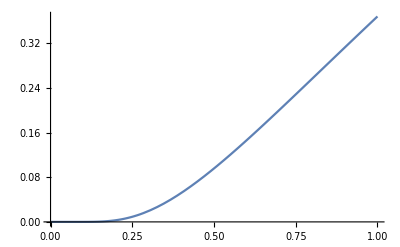

```mathematica
Plot[Exp[-1/x] √x,{x,0,1}]
```

```mathematica
ComplexExpand[Im[ⅈ Exp[1/x] √(ⅈ x)]]
```

ⅇ^(1/x) (x^2)^(1/4) Cos[1/2 Arg[ⅈ x]]

```mathematica
Plot3D[Evaluate[Im[ⅈ Exp[1/x] √(x^2)]/.x->x+ⅈ y],{x,-5,5},{y,-5,5}]
```

-Graphics3D-

```mathematica
itest/.x->x+ⅈ 0.0000001/.x->-4
```

-0.144064+5.86806×10^-9 ⅈ

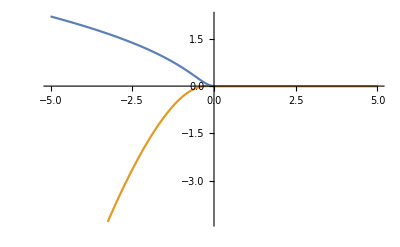

```mathematica
Plot[Evaluate@{Im[-itest/.x->y+ⅈ 0.000001],-(-y)^(3/2) Exp[1/y]HeavisideTheta[-y]},{y,-5,5}]
```

```mathematica
ComplexPlot[itest,{x,-1-ⅈ,1+ⅈ}]
```

-Graphics-

General::munfl: Exp[-1797.19] is too small to represent as a normalized machine number; precision may be lost.

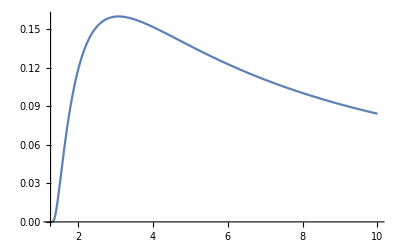

```mathematica
Plot[((x-θc) Exp[-1/(B(x-θc))])/x^2/.{θc->1.27,B->3.12},{x,1.27,10}]
```

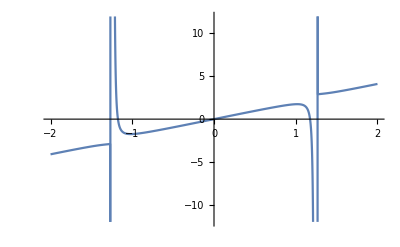

```mathematica
Plot[Evaluate@Im[ⅈ Sign[Im[θ+ ⅈ 10^-5]]iF1[θc,B][θ+ⅈ 10^-5]-ⅈ Sign[Im[θ+ ⅈ 10^-5]]iF1[θc,B][-(θ+ⅈ 10^-5)]]/.{θc->1.27,B->3.12},{θ,-2,2}]
```

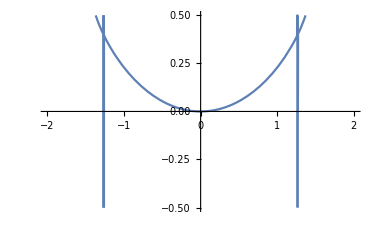

```mathematica
Plot[Evaluate@Re[(iii+ⅈ Sign[Im[θ]]iF1[θc,B][θ]-ⅈ Sign[Im[θ]]iF1[θc,B][-θ])/.θ->x+10^-7 ⅈ]/.{θc->1.27,B->3.12},{x,-2,2},PlotRange->{-0.5,0.5}]
```

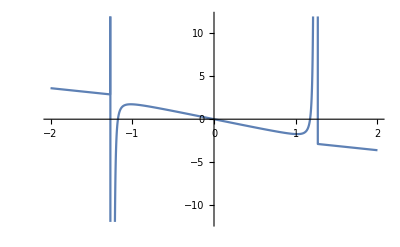

```mathematica
Plot[Evaluate@Im[(iii/.θ->θ+ⅈ 10^-5)]/.{θc->1.27,B->3.12},{θ,-2,2}]
```

```mathematica
Evaluate[Im[(θ^2+0.2^2)^(5/6)(iii+ⅈ θ/Abs[1[θc,B][θ]-ⅈ Sign[Im[θ]]iF1[θc,B][-θ])/.{θc->1.27,B->3.12}/.θ->x+ⅈ y]]/.{x->1.1,y->0.3}
```

0.325779

```mathematica
Series[x Exp[1/x],{x,∞,0}]
```

x+1+O[1/x]^1

```mathematica
iii2=Integrate[(x Exp[1/x])/x^2 1/(x+y),{x,x0,∞},Assumptions->{y<x0,y>0,x0>0}]
```

(ⅇ^(-1/y) (ExpIntegralEi[1/x0+1/y]-ExpIntegralEi[1/y]))/y

```mathematica
FullSimplify[iii,Assumptions->{x0>0,y>0,y<x0}]
```

1/(x0 y^2)(-2 ⅇ^(1/x0) (-1+x0) y ExpIntegralEi[-1/x0]+x0 (2 y-ⅇ^(1/(x0-y)) (x0-y) ExpIntegralEi[1/(-x0+y)]+ⅇ^(1/(x0+y)) (x0+y) ExpIntegralEi[-1/(x0+y)]))

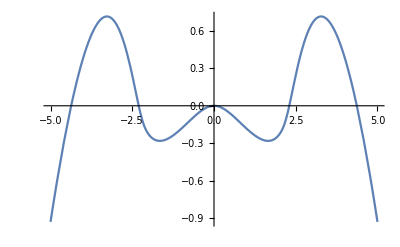

```mathematica
Plot[y^2 Re@(iii)-0.2 y^2 ii/.x0->2/.θ0->0.5,{y,-5,5}]
```

```mathematica
ComplexExpand[(1-θ^2/θc^2)(θ-0.1 θ^3)(1-θ^2)^(-15/8)/.θ->ⅈ θ]
```

0.+ⅈ (θ/((1+θ^2)^(15/8))+(0.1 θ^3)/((1+θ^2)^(15/8))+θ^3/((1+θ^2)^(15/8) θc^2)+(0.1 θ^5)/((1+θ^2)^(15/8) θc^2))

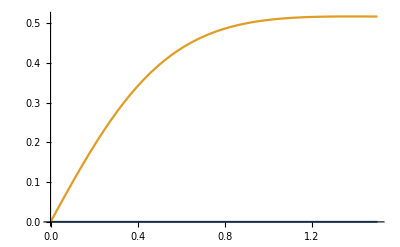

```mathematica
Plot[Evaluate@ReIm[(1-θ^2/θc^2)(θ-0.1 θ^3)(1-θ^2)^(-15/8)/.θ->ⅈ θ/.θc->1.2],{θ,0, 1.5}]
```

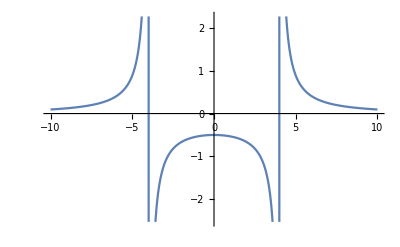

```mathematica
Plot[1/(x-y)-1/(x+y)/.y->4,{x,-10,10}]
```

```mathematica
iiii=Integrate[D[((-θ0^2-(ⅈ θ)^2)^(5/6))/(θ^2+θp^2),θp],θp]
```

((θ^2-θ0^2)^(5/6))/(θ^2+θp^2)

```mathematica
Simplify[ComplexExpand[Im[(iii+ⅈ Sign[Im[θ]] iF1[θc,B][θ]-ⅈ Sign[Im[θ]]iF1[θc,B][-θ])/.θ->ⅈ θ],TargetFunctions->Conjugate],Assumptions->{θ>0,θc>0,B>0}]
```

0

```mathematica
ii=Integrate[(iF1[θc,B][ⅈ θ])/((θ+y)θ^2),{θ,θ0,∞},Assumptions->{y>0,θ0>0,B>0,θc>0}]
```

```mathematica
ii=Integrate[((θ^2-θ0^2)^(5/6))/((θ+y)θ^2),{θ,θ0,∞},Assumptions->{y>0,θp∈Reals}]
```

ConditionalExpression[(π (-θ0^(5/3)+(y^2+θ0^2)^(5/6)))/y^2, Re[θ0]>0&&Im[θ0]==0]

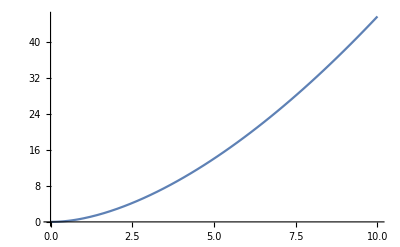

```mathematica
Plot[(1+x^2)^(5/6)-1,{x,0,10}]
```

```mathematica
Plot[y^2 ii/.{θ0->0.18},{θp,0,1}]
```

-Graphics-

```mathematica
i0=Limit[θp^2+3 θp^4+0.8 θp^6+x Exp[1/x]ExpIntegralEi[-1/x]+y Exp[1/y]ExpIntegralEi[-1/y]+ii/.{θ0->0.18,x->θp-0.5,y->-0.5-θp},θp->0]
```

3.96624

```mathematica
ComplexPlot[(θp^2+3 θp^4+0.8 θp^6+x Exp[1/x]ExpIntegralEi[-1/x]+y Exp[1/y]ExpIntegralEi[-1/y]+ii/.{θ0->0.18,x->θp-0.5,y->-0.5-θp})-i0,{θp,-1.5-1.5ⅈ,1.5+1.5ⅈ}]
```

-Graphics-

```mathematica
Integrate[(θ0
```

```mathematica
Integrate[1/(θ^2+θp^2),θ]
```

ArcTan[θ/θp]/θp

```mathematica
2/(15/8)
```

16/15

```mathematica
2/(0.326419 4.78984)
```

1.27919

```mathematica
Series[1/((θ-θc) h'[θ](1-θ)^(-15/8)),{θ,θc,0}]
```

(1-θc)^(15/8)/(h'[θc] (θ-θc))+(-(15 (1-θc)^(7/8))/(8 h'[θc])-((1-θc)^(15/8) h''[θc])/h'[θc]^2)+O[θ-θc]^1